## Chapter 8 problems

### Constants

```mathematica
hbar=1.0545718×10^-34
```

1.05457×10^-34

```mathematica
e0=8.85418782×10^-12
```

8.85419×10^-12

```mathematica
mu0=1.2566370614×10^-6
```

1.25664×10^-6

```mathematica
1/Sqrt[mu0 e0]
```

2.99792×10^8

```mathematica
me=9.10938356×10^-31
```

9.10938×10^-31

```mathematica
muonmass=105.6583715 10^6 ee/c^2
```

1.87837×10^-28

```mathematica
c= 3 10^8
```

300000000

```mathematica
ee=1.6 10^-19
```

1.6×10^-19

```mathematica
alpha =ee^2/(4 Pi e0 hbar c)
```

0.0072725

```mathematica
137 alpha
```

0.996333

Bohr Radius

```mathematica
a0=4 Pi e0 hbar^2/(ee^2 me)
```

5.30618×10^-11

Rydberg Constant

```mathematica
Ry=hbar^2/(2 me a0^2)
```

2.16805×10^-18

```mathematica
Ry/ee
```

13.5503

### Airy functions

```mathematica
AiryAi[0]
```

1/(3^(2/3) Gamma[2/3])

```mathematica
AiryBi[0]
```

1/(3^(1/6) Gamma[2/3])

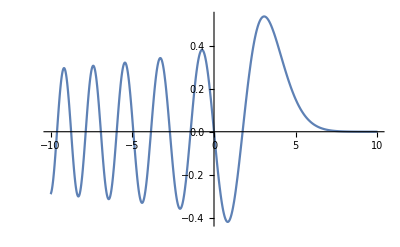

```mathematica
Plot[AiryAi[x+AiryAiZero[2]],{x,-10,10}]
```

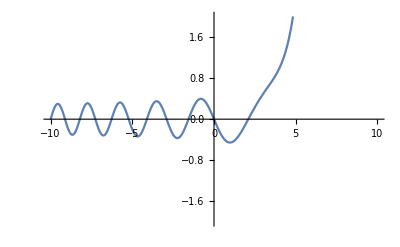

```mathematica
Plot[AiryBi[x+AiryBiZero[2]],{x,-10,10},PlotRange->{{-10,10},{-2,2}}]
```

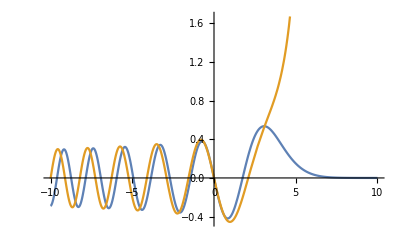

```mathematica
Plot[{AiryAi[x+AiryAiZero[2]],AiryBi[x+AiryBiZero[2]]},{x,-10,10}]
```

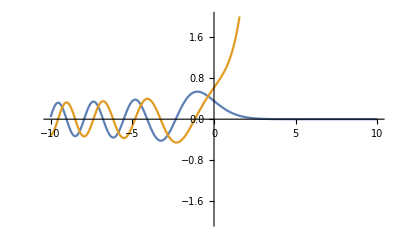

```mathematica
Plot[{AiryAi[x],AiryBi[x]},{x,-10,10},PlotRange->{{-10,10},{-2,2}}]
```

### 8.1

Here is the series expansion

```mathematica
Series[Sqrt[1-x],{x,0,3}]
```

1-x/2-x^2/8-x^3/16+O[x]^4

Now we have a question - what is the second order in energy correction?

Matrix Elements

```mathematica
Assuming[{m∈Integers,n∈Integers},(2V0)/L Integrate[Sin[n Pi x/L]Sin[m Pi x/L],{x,0,L/2}]]
```

(2 V0 (L n Cos[(n π)/2] Sin[(m π)/2]-L m Cos[(m π)/2] Sin[(n π)/2]))/(L (m^2 π-n^2 π))

This is gonna be a mess.

### 8.5

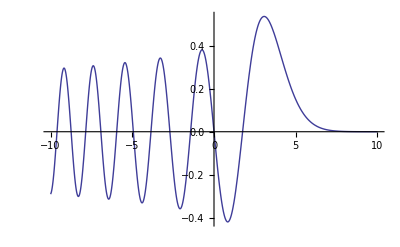

```mathematica
Plot[AiryAi[x+AiryAiZero[2]],{x,-10,10}]
```

#### c)

The energies are alpha z_n mg

```mathematica
hbar=1.0545718×10^-34
```

1.05457×10^-34

```mathematica
alpha[m_,g_,hbar_]:= ((2 m^2 g)/hbar^2)^(1/3)
```

```mathematica
Table[N[AiryAiZero[n]],{n,1,10}]
```

{-2.33811,-4.08795,-5.52056,-6.78671,-7.94413,-9.02265,-10.0402,-11.0085,-11.936,-12.8288}

```mathematica
Table[- N[(9.8 0.1AiryAiZero[n])/alpha[0.1,9.8,hbar],3],{n,1,4}]
```

{8.80486×10^-23,1.53944×10^-22,2.07894×10^-22,2.55574×10^-22}

#### d)

```mathematica
me=9.10938356×10^(-31)
```

9.10938×10^-31

```mathematica
ee=1.60217662×10^-19
```

1.60218×10^-19

```mathematica
- 9.8 me/ee AiryAiZero[1]/alpha[me,9.8,hbar]
```

1.14774×10^-13

Virial thm implies <T>=<V>/2

```mathematica
2(- 9.8 me AiryAiZero[1])/(3 me 9.8alpha[me,9.8,hbar])
```

0.00137324

### Problem 8.6

```mathematica
Integrate[Sqrt[1-y],{y,0,1}]
```

2/3

```mathematica
EWKB[n_]:=(3/2 9.81 Sqrt[0.1/2]hbar Pi)^(2/3)(n-1/4)^(2/3)
```

```mathematica
Table[EWKB[n],{n,1,4}]
```

{8.74356×10^-23,1.53818×10^-22,2.07907×10^-22,2.55663×10^-22}

Here are the exact results

```mathematica
Table[- N[(9.8 0.1AiryAiZero[n])/alpha[0.1,9.8,hbar],3],{n,1,4}]
```

{8.80486×10^-23,1.53944×10^-22,2.07894×10^-22,2.55574×10^-22}

Here’s the relative errors in WKB

```mathematica
Clear[alpha]
```

```mathematica
alpha[m_,g_,hbar_]:= ((2 m^2 g)/hbar^2)^(1/3)
```

```mathematica
Table[(- N[(9.8 0.1AiryAiZero[n])/alpha[0.1,9.8,hbar],3]-EWKB[n])/(- N[(9.8 0.1AiryAiZero[n])/alpha[0.1,9.8,hbar],3]),{n,1,100}]
```

{0.00696225,0.000822701,-0.0000645912,-0.000347868,-0.000472702,-0.000538459,-0.000577279,-0.000602089,-0.000618899,-0.000630812,-0.000639561,-0.000646173,-0.000651293,-0.000655337,-0.000658588,-0.000661239,-0.00066343,-0.000665261,-0.000666807,-0.000668125,-0.000669256,-0.000670235,-0.000671088,-0.000671836,-0.000672494,-0.000673078,-0.000673597,-0.000674061,-0.000674478,-0.000674853,-0.000675193,-0.0006755,-0.00067578,-0.000676036,-0.00067627,-0.000676484,-0.000676681,-0.000676863,-0.000677031,-0.000677186,-0.00067733,-0.000677464,-0.000677588,-0.000677704,-0.000677813,-0.000677914,-0.000678009,-0.000678098,-0.000678181,-0.00067826,-0.000678334,-0.000678404,-0.00067847,-0.000678532,-0.000678591,-0.000678646,-0.000678699,-0.000678749,-0.000678797,-0.000678842,-0.000678885,-0.000678925,-0.000678964,-0.000679001,-0.000679037,-0.000679071,-0.000679103,-0.000679134,-0.000679163,-0.000679192,-0.000679219,-0.000679245,-0.00067927,-0.000679293,-0.000679316,-0.000679338,-0.00067936,-0.00067938,-0.0006794,-0.000679418,-0.000679437,-0.000679454,-0.000679471,-0.000679487,-0.000679503,-0.000679518,-0.000679533,-0.000679547,-0.000679561,-0.000679574,-0.000679587,-0.000679599,-0.000679611,-0.000679622,-0.000679634,-0.000679644,-0.000679655,-0.000679665,-0.000679675,-0.000679685}

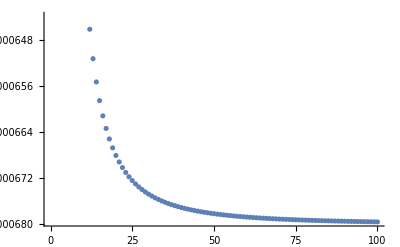

```mathematica
ListPlot[Table[(- N[(9.8 0.1AiryAiZero[n])/alpha[0.1,9.8,hbar],3]-EWKB[n])/(- N[(9.8 0.1AiryAiZero[n])/alpha[0.1,9.8,hbar],3]),{n,1,100}]]
```

c) How big would n have to be for the ball to have an average height of 1m above the ground?

### Problem 8.8

```mathematica
Table[0.1 2^(1/3)(2n+1)^(2/3),{n,123,128}]
```

{4.95992,4.98666,5.01332,5.03992,5.06645,5.0929}

### Problem 8.10

### Problem 8.12

This is a really miserable problem

Use the WKB to find the bound state energy for the problem in 2.51

```mathematica
V[x_,hbar_,a_,m_]:=-(hbar^2 a^2)/m Sech[a x]^2
```

```mathematica
Sqrt[2m(EE-V[x,hbar,a,m])]
```

√2 √(m (EE+(a^2 hbar^2 Sech[a x]^2)/m))

Substitute z = Sech[a (x])^2

```mathematica
D[Sech[a x]^2,{x,1}]
```

-2 a Sech[a x]^2 Tanh[a x]

```mathematica
(Sqrt[2m(EE-V[x,hbar,a,m])]/.{Sech[a x]^2->z})/D[Sech[a x]^2,{x,1}]
```

-(√(m (EE+(a^2 hbar^2 z)/m)) Cosh[a x]^2 Coth[a x])/(√2 a)

```mathematica
-(√(m (EE+(a^2 hbar^2 z)/m)) Cosh[a x]^2 Coth[a x])/(√2 a)/.{Cosh[a x]^2->1/z}
```

-(√(m (EE+(a^2 hbar^2 z)/m)) Coth[a x])/(√2 a z)

```mathematica
-(√(m (EE+(a^2 hbar^2 z)/m)) Coth[a x])/(√2 a z)/.{Coth[a x]->1/Sqrt[1-z]}
```

-(√(m (EE+(a^2 hbar^2 z)/m)))/(√2 a √(1-z) z)

Turning points

```mathematica
Clear[EE]
```

```mathematica
Energy=-(a^2 hbar^2)/m zb
```

-(a^2 hbar^2 zb)/m

```mathematica
Assuming[{Sqrt[a^2 hbar^2]==a hbar},FullSimplify[-(√(m (EE+(a^2 hbar^2 z)/m)))/(√2 a √(1-z) z)/.{EE->-(a^2 hbar^2)/m zb}]]
```

-(√(a^2 hbar^2 (z-zb)))/(a √(2-2 z) z)

```mathematica
hbar/Sqrt[2] Assuming[zb>1,2Integrate[(√(z-zb))/(√(1-z) z),{z,zb,1}]]
```

√2 hbar (π-π √zb)

```mathematica
Clear[zb]
```

```mathematica
FullSimplify[ √2 hbar (π-π √zb)/.{zb->m Abs[ee]/(a^2 hbar^2)}]
```

√2 hbar (π-√(m/(a^2 hbar^2)) π √Abs[ee])

Now this is equal to (n-1/2)Pi hbar, so we have for n=1

```mathematica
Solve[√2 hbar (π-√(m/(a^2 hbar^2)) π √Abs[ee])==Pi hbar/2,ee]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ee→-((-9+4 √2) a^2 hbar^2)/(8 m)},{ee→((-9+4 √2) a^2 hbar^2)/(8 m)}}

```mathematica
FullSimplify[-(-9+4 √2)/8]
```

9/8-1/(√2)

```mathematica
N[9/8-1/Sqrt[2]]
```

0.417893

### Problem 8.13

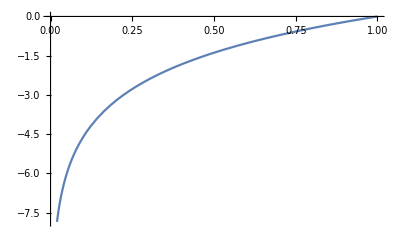

```mathematica
Plot[2Log[x],{x,0,1}]
```

### Problem 8.14

c)

```mathematica
Series[Tan[x],{x,0,3}]
```

x+x^3/3+O[x]^4

```mathematica
Assuming[{Tan[n Pi]==0,n∈Integers},Series[Tan[(n+1/2)Pi+y],{y,0,3}]]/.Tan[n Pi]->0
```

-1/y+y/3+y^3/45+O[y]^4

d)

```mathematica
VV[x_,a_,m_,ω_]:=If[x<0,1/2 m ω^2(x+a)^2,1/2 m ω^2(x-a)^2]
```

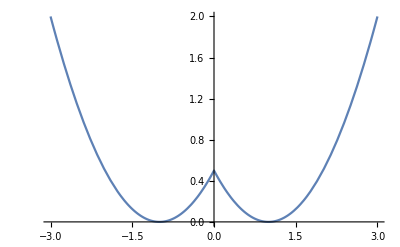

```mathematica
Plot[VV[x,1,1,1],{x,-3,3}]
```

```mathematica
Integrate[Sqrt[1-y^2],{y,-1,1}]
```

π/2

```mathematica
Assuming[Re[a^2/y0^2]>1,Integrate[Sqrt[1-w^2],{w,-a/y0,-1}]]
```

ConditionalExpression[(ⅈ a √(-1+a^2/y0^2))/(2 y0)-1/2 ArcCos[a/y0],a y0>y0^2]

```mathematica
Assuming[{Im[y0]==0,Im[x1]==0,x1>0,y0>0},Integrate[w Sqrt[1-w^2],{w,1,y0/(y0+x1)}]]
```

-(x1 (x1+2 y0))^(3/2)/(3 (x1+y0)^3)

```mathematica
Integrate[Sqrt[y^2-y0^2],{y,y0,a}]
```

ConditionalExpression[1/2 (a √((a-y0) (a+y0))+y0^2 (Log[y0]-Log[a+√(a^2-y0^2)])),y0^2+Conjugate[y0]^2≤a^2+Conjugate[a]^2&&((y0/(a-y0)≠0&&Re[y0/(a-y0)]≥0)||y0/(a-y0)∉Reals||Re[y0/(a-y0)]<-1)]

```mathematica
Assuming[{a>y0,y0>0},Integrate[Sqrt[y^2-y0^2],{y,y0,a}]]
```

1/2 (a √(a^2-y0^2)+y0^2 Log[y0/(a+√(a^2-y0^2))])

```mathematica
Series[Sqrt[1-x^2],{x,0,3}]
```

1-x^2/2+O[x]^4

### Morse Potential

```mathematica
MP[x_,a_,D0_,x0_]:=D0(Exp[-2a(x-x0)]-2Exp[-a(x-x0)])
```

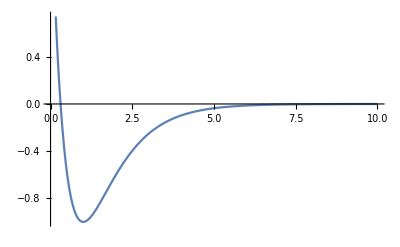

```mathematica
Plot[MP[x,1,1,1],{x,0,10}]
```

```mathematica
xp[a_,D0_,x0_,En_]:=x0-1/a Log[1+Sqrt[1+En/D0]]
```

```mathematica
xm[a_,D0_,x0_,En_]:=x0-1/a Log[1-Sqrt[1+En/D0]]
```

The roots of the transcendental equation must be positive also

```mathematica
FullSimplify[Exp[-a xp[a,D0,x0,En]]]
```

ⅇ^(-a x0) (1+√((D0+En)/D0))

```mathematica
exp[a_,D0_,x0_,En_]:=ⅇ^(-a x0) (1+√((D0+En)/D0))
```

```mathematica
FullSimplify[Exp[-a xm[a,D0,x0,En]]]
```

-ⅇ^(-a x0) (-1+√((D0+En)/D0))

```mathematica
exm[a_,D0_,x0_,En_]:=ⅇ^(-a x0) (1-√((D0+En)/D0))
```

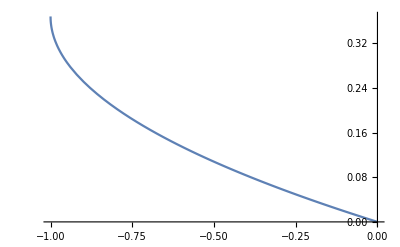

```mathematica
Plot[ exm[1,1,1,En],{En,0,-1}]
```

```mathematica
gr[En_,D0_,x0_,a_]:=Line[{{xm[a,D0,x0,En],En},{xp[a,D0,x0,En],En}}]
```

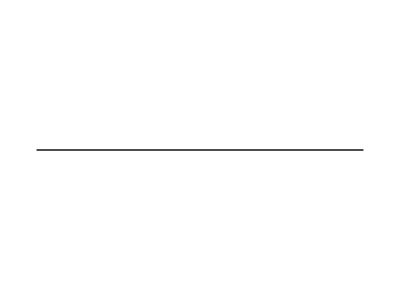

```mathematica
Show[Graphics[gr[-1/2,1,1,1]]]
```

```mathematica
Manipulate[Show[{Plot[MP[x,1,1,1],{x,0,10}],Graphics[gr[En,1,1,1]]}],{En,-1,0}]
```

```mathematica
Assuming[{wp>wm,wp∈Reals,wm∈Reals,wp>0,wm>0},Integrate[Sqrt[(w-wp)(wm-w)]/w,{w,wp,wm}]]
```

π √(wm wp)-1/2 π (wm+wp)

```mathematica
N[1/2(Sqrt[2]-1)]
```

0.207107

Let’s plot the energy eigenvalues for the case where the minimum value of the potential is -D0

```mathematica
spec1[n_,D0_,hbar_,a_,m_]:=-D0+(n+1/2)hbar a Sqrt[(2D0)/m]-(n+1/2)^2(hbar^2 a^2)/(2m)
```

```mathematica
nmax[D0_,hbar_,a_,m_]:=Floor[Sqrt[2m D0]/(hbar a)]
```

```mathematica
nmax[5,1,1,1]
```

3

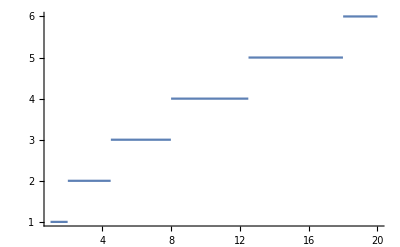

```mathematica
Plot[nmax[y,1,1,1],{y,1,20}]
```

```mathematica
Table[N[spec1[n,5,1,1,1]],{n,0,nmax[5,1,1,1]}]
```

{-3.54386,-1.38158,-0.219306,-0.0570282}

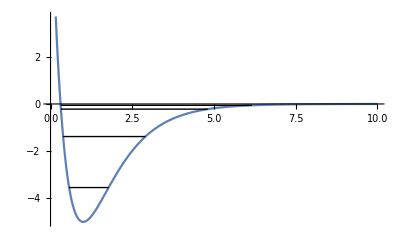

```mathematica
Show[{Plot[MP[x,1,5,1],{x,0,10}],Table[Graphics[gr[N[spec1[n,5,1,1,1]],5,1,1]],{n,0,nmax[5,1,1,1]}]}]
```

```mathematica
Manipulate[Show[{Plot[MP[x,1,D0,1],{x,0,10},PlotRange->{{0,8},{-20,5}}],Table[Graphics[gr[N[spec1[n,D0,1,1,1]],D0,1,1]],{n,0,nmax[D0,1,1,1]}]}],{D0,1,20}]
```

Compare this with the other form for the Morse potential

```mathematica
MP2[x_,a_,D0_,x0_]:=D0(1-Exp[-a(x-x0)])^2
```

This is just a shifted

```mathematica
FullSimplify[MP[x,a,D0,x0]+D0]
```

D0 (-1+ⅇ^(a (-x+x0)))^2

```mathematica
spec1[n,D0,hbar,a,m]+D0
```

√2 a hbar √(D0/m) (1/2+n)-(a^2 hbar^2 (1/2+n)^2)/(2 m)

This is the incorrect expression from Wikipedia

```mathematica
spec2[n_,a_,D0_,hbar_,m_]:=(a^2 hbar^2)/(2m)(1-(a^2 hbar^2)/(2m D0)(Sqrt[2 m D0]/(a hbar)-n-1/2)^2)
```

```mathematica
xm2[a_,D0_,x0_,En_]:=x0-1/a Log[1-Sqrt[En/D0]]
```

```mathematica
xp2[a_,D0_,x0_,En_]:=x0-1/a Log[1+Sqrt[En/D0]]
```

```mathematica
gr2[En_,D0_,x0_,a_]:=Line[{{xm2[a,D0,x0,En],En},{xp2[a,D0,x0,En],En}}]
```

```mathematica
Manipulate[Show[{Plot[MP2[x,1,1,1],{x,0,10}],Graphics[gr2[En,1,1,1]]}],{En,0,1}]
```

```mathematica
N[spec2[2,1,1,1,1]]
```

0.205267

```mathematica
N[spec2[1,1,1,1,1]]
```

0.49816

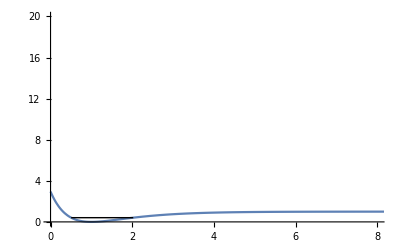

```mathematica
Show[{Plot[MP2[x,1,1,1],{x,0,10},PlotRange->{{0,8},{0,20}}],Graphics[gr2[N[spec1[2,1,1,1,1]+1],1,1,1]]}]
```

```mathematica
Manipulate[Show[{Plot[MP2[x,1,D0,1],{x,0,10},PlotRange->{{0,8},{0,20}}],Table[Graphics[gr2[N[spec1[n,D0,1,1,1]+D0],D0,1,1]],{n,0,nmax[D0,1,1,1]}]}],{D0,1,20}]
```

```mathematica
D[MP[x,a,D0,x0],{x,2}]/.x->x0
```

2 a^2 D0

A bit easier to Taylor expand and then read off 1/2 m omega^2

```mathematica
Series[MP[x,a,D0,x0],{x,x0,2}]
```

-D0+a^2 D0 (x-x0)^2+O[x-x0]^3

```mathematica
omega[a_,D0_,x0_,m_]:=a Sqrt[(2D0)/m]
```

```mathematica
1/2 m (a Sqrt[(2D0)/m])^2
```

a^2 D0

Look at the spectrum

```mathematica
spec1[n,D0,hbar,a,m]+D0
```

√2 a hbar √(D0/m) (1/2+n)-(a^2 hbar^2 (1/2+n)^2)/(2 m)

Check this is correct

```mathematica
Assuming[{D0∈Reals,D0>0,m∈Reals,m>0},FullSimplify[(hbar ω (1/2+n)(1 -(hbar ω)/(4D0)(n+1/2))/.ω->a Sqrt[(2D0)/m])- (spec1[n,D0,hbar,a,m]+D0)]]
```

0

Here’s the energy

```mathematica
hbar ω (1/2+n)(1 -(hbar ω)/(4D0)(n+1/2))
```

hbar (1/2+n) ω (1-(hbar (1/2+n) ω)/(4 D0))

It is given by

```mathematica
Subscript[E, n](1-Subscript[E, n]/(4 Subscript[D, 0]))
```

ⅇ_n (1-ⅇ_n/(4 D_0))

Hence if hbar ω << 4D0 then the low lying levels look harmonic.

```mathematica
hbar a Sqrt[(2D0)/m]<< 4 D0
```

Get::noopen: Cannot open 4.

√2 a D0 hbar √(D0/m) $Failed

```mathematica
hbar a^2 D0/m<< 8  D0^2
```

Get::noopen: Cannot open 8.

(a^2 D0^3 hbar $Failed)/m

Condition for harmonic low lying levels:

```mathematica
hbar a^2/(8m)<<D0
```

Get::noopen: Cannot open D0.

(a^2 hbar $Failed)/(8 m)

```mathematica
FullSimplify[spec1[n+1,D0,hbar,a,m]-spec1[n,D0,hbar,a,m]]
```

-(a hbar (-√2 √(D0/m) m+a hbar (1+n)))/m

Use

```mathematica
hbar ω (1- (hbar ω)/(2D0)(n+1))/.ω->a Sqrt[(2D0)/m]
```

√2 a hbar √(D0/m) (1-(a hbar √(D0/m) (1+n))/(√2 D0))

Check this is correct

```mathematica
FullSimplify[-(a hbar (-√2 √(D0/m) m+a hbar (1+n)))/m-(√2 a hbar √(D0/m) (1-(a hbar √(D0/m) (1+n))/(√2 D0)))]
```

0

```mathematica
de[n_,hbar_,m_,a_,D0_]:=√2 a hbar √(D0/m) (1-(a hbar √(D0/m) (1+n))/(√2 D0))
```

```mathematica
Table[N[de[n,1,1,1,100]],{n,0,nmax[100,1,1,1]}]
```

{13.1421,12.1421,11.1421,10.1421,9.14214,8.14214,7.14214,6.14214,5.14214,4.14214,3.14214,2.14214,1.14214,0.142136,-0.857864}

```mathematica
Table[N[de[n,1,1,1,1000]],{n,0,nmax[1000,1,1,1]}]
```

{43.7214,42.7214,41.7214,40.7214,39.7214,38.7214,37.7214,36.7214,35.7214,34.7214,33.7214,32.7214,31.7214,30.7214,29.7214,28.7214,27.7214,26.7214,25.7214,24.7214,23.7214,22.7214,21.7214,20.7214,19.7214,18.7214,17.7214,16.7214,15.7214,14.7214,13.7214,12.7214,11.7214,10.7214,9.72136,8.72136,7.72136,6.72136,5.72136,4.72136,3.72136,2.72136,1.72136,0.72136,-0.27864}

Tunneling

```mathematica
Assuming[{wp>wm,wp∈Reals,wm∈Reals,wp>0,wm>0},Integrate[Sqrt[-(w-wp)(wm-w)]/w,{w,wm,0}]]
```

Integrate::idiv: Integral of (√((-w+wm) (-w+wp)))/w does not converge on {wm,0}.

∫_wm^0 (√((-w+wm) (-w+wp)))/w ⅆw

### Gamow alpha decay

```mathematica
r2[Eem_,Z_]:=2 Z/(4 Pi e0) ee/(Eem 10^6)/10^-15
```

```mathematica
r2[4.2,91]
```

(3.44836×10^9 ee)/e0

```mathematica
r2[7,90]
```

(45000000000 ee)/(7 e0 π)

```mathematica
r2[7,84]
```

(6000000000 ee)/(e0 π)

### Muon Catalyzed Fusion

```mathematica
muonmass=105.6583715 10^6 ee/c^2
```

(1.05658×10^8 ee)/c^2

```mathematica
V[x_]:=1/x-1.5/(1+0.127 x)^4
```

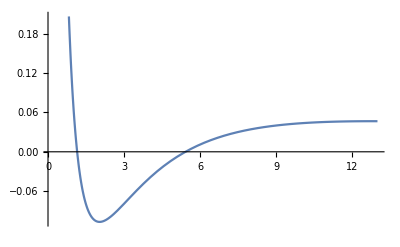

```mathematica
Plot[V[x],{x,0.1,13}]
```

```mathematica
D[V[x],{x,1}]
```

0.762/(1+0.127 x)^5-1/x^2

```mathematica
(1+0.127 x)^5 x^2 D[V[x],{x,1}]
```

(0.762/(1+0.127 x)^5-1/x^2) (1+0.127 x)^5 x^2

```mathematica
Solve[Expand[0.762 x^2-(1+0.127 x)^5]==0&&x>0&&x<10,x,Reals]
```

{{x→2.03542}}

```mathematica
x0=2.035420908926528
```

2.03542

```mathematica
V[x0]
```

-0.106673

Here is the curvature at the minimum

```mathematica
D[V[x],{x,2}]/.x->x0
```

0.115384

```mathematica
Sqrt[D[V[x],{x,2}]/.x->x0]
```

0.339682

```mathematica
Sqrt[0.11538385679622122]
```

0.339682

```mathematica
(4Pi e0 hbar^2)/(muonmass ee^2)
```

(1.18934×10^-7 c^2 e0 hbar^2)/ee^3

```mathematica
(4Pi e0 hbar^2)/(muonmass ee^2)x0
```

(2.42081×10^-7 c^2 e0 hbar^2)/ee^3

```mathematica
(4Pi e0 hbar^2)/(muonmass ee^2)x0/10^-14
```

(2.42081×10^7 c^2 e0 hbar^2)/ee^3

```mathematica
1.3 10^-10/200
```

6.5×10^-13

```mathematica
(4Pi e0 hbar^2)/(me ee^2)
```

(4 e0 hbar^2 π)/(ee^2 me)

### x^4

```mathematica
Integrate[Sqrt[1-x^2],{x,0,1}]
```

π/4

```mathematica
N[Integrate[Sqrt[1-x^4],{x,0,1}]]
```

0.874019

### Eckart Barrier

```mathematica
VEck[x_,a_,A_,B_]:=A Exp[2 Pi x/a]/(1+Exp[2 Pi x/a])+B Exp[2 Pi x/a]/(1+Exp[2 Pi x/a])^2
```

Reproduce fi

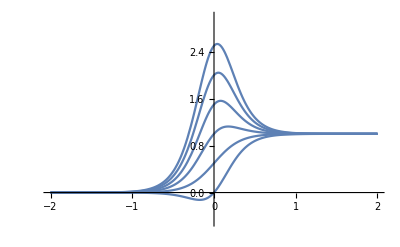

```mathematica
Plot[Table[VEck[x,1,1,B],{B,-2,8,2}],{x,-2,2},PlotRange->{{-2,2},{-0.5,3}}]
```

```mathematica
FullSimplify[VEck[x,a,0,Subscript[V, 0]]]
```

1/4 Sech[(π x)/a]^2 V_0

```mathematica
FullSimplify[VEck[x,a,0,4 Subscript[V, 0]]]
```

Sech[(π x)/a]^2 V_0